```mathematica
Solve[z==r^2 (u+2/x),x]
```

```mathematica
{{x->-(2 r^2)/(r^2 u-z)}}
```

```mathematica
D[-(2 r^2)/(r^2 u-z),z]
```

-(2 r^2)/((r^2 u-z)^2)

```mathematica
Infinity
```

∞

```mathematica
MeijerGReduce[(z+C)^-4,z]
```

ConditionalExpression[MeijerG[{{-3},{}},{{0},{}},z/C]/(6 C^4),Re[C]>0]

```mathematica
MeijerG[{{},{}},{{3/2},{-3/2}},z]
```

```mathematica
1/(C+z)^4=(Subscript[G, 1,1]^(1,1)(z/C|{{-3}, {0}}))/(6 C^4)
```

```mathematica
32 √z=Subscript[G, 0,2]^(1,0)(z|{{3/2,-3/2}})
```

BesselJ[3,2 √z]

```mathematica
Integrate[MeijerG[{{-3},{}},{{0},{}},z/C]MeijerG[{{},{}},{{3},{0}},z],{z,0,Infinity}]
```

ConditionalExpression[2 C^4 BesselK[0,2 √C],Im[C]≠0||Re[C]≥0]

```mathematica
2 C^4 02 √C
```

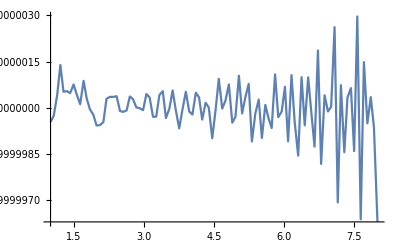

```mathematica
Plot[(16/(3))BesselK[0,0.8109599250271249 r]/(2 r^-3 Sum[x^2 Sqrt[-0.164414+2/Max[x,0.00005]]^3 BesselJ[3,2r Sqrt[-0.164414+2/Max[x,0.00005]]](0.0001),{x,0,2/0.164414,0.0001}]),{r,1,8},PlotLegends->"Expressions",PlotRange->All,MaxRecursion->0,PlotPoints->100]
```